## GRAPE` Documentation

## Preamble

```mathematica
Needs["GRAPE`"]
Needs["QuantumUtils`"]
```

Attributes::attnf: HoldRestComplete is not a known attribute.

SetDelayed::write: Tag NormalMatrixQ in NormalMatrixQ[M_] is Protected.

SetDelayed::write: Tag SquareMatrixQ in SquareMatrixQ[M_] is Protected.

Get::noopen: Cannot open "Superoperator`".

Needs::nocont: Context "Superoperator`" was not created when Needs was evaluated.

## Introduction and Overview

QSim` is a general purpose quantum system time-evolution simulator whose primary objective is ease of use. This is in keeping with one of Mathematica’s main advantages over most other languages; rapid and intuitive development of ideas with minimal overhead. A description of the the quantum system, usually a Hamiltonian, and an action on that quantum system are provided, and some observable, quantum state, propogator, etc. is monitored as the system evolves.

As a quick example, the following computes the expectation value of X⊗Y of the initial state |00⟩ undergoing evolution with the time-dependent Hamiltonian H(t)=cos(t)X⊗X+sin(t)Y⊗Y.

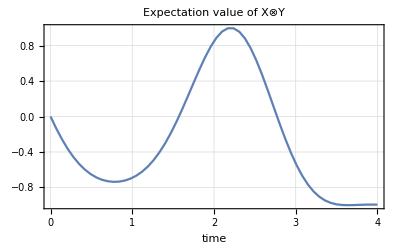

```mathematica
ListPlot[
Observables[EvalPulse[Cos[#]X⊗X+Sin[#]Y⊗Y&,4,PollingInterval->0.1,InitialState->Projector[{1,0,0,0}],Observables->{X⊗Y}],TimeVector->True],
Joined->True,PlotRange->All,PlotTheme->"Detailed",
PlotLabel->"Expectation value of X⊗Y",FrameLabel->{"time",None}
]
```

## Single Pulse Evaluator

The workhorse of QSim` is EvalPulse, which has two non-optional arguments, EvalPulse[H,p], where H is a Hamiltonian and p is an action, or “pulse”. There are four types of “pulses” that can be entered:

Type | Predicate | Description
Drift pulse | DriftPulseQ | Evolution under the Hamiltonian for some time. In this case, p is just equal to a number,or a Symbol such as t.
Shaped pulse | ShapedPulseQ | A list of control Hamiltonians,time spacings,and amplitudes is provided, and everything is simulated. In this case, 
p is of the form {pulse,{Hctl1,Hctl2,...}} where pulse is either a text file (eg. CVS) containing the shaped pulse, or the 
shaped pulse itself. A shaped pulse is of the form 
{dt1,a11,a12,a13,...},{dt2,a21,a22,a23,...},{dt2,a21,a22,a23,...},...}.
Unitary pulse | UnitaryPulseQ | The Hamiltonian is ignored and some other unitary is applied. This kind of pulse only really makes within pulse sequences. 
In this case, p is of the form {U,t} where U is the unitary matrix and t is how much time the pulse should take.
Channel pulse | ChannelPulseQ | The Hamiltonian is ignored, and the supplied superoperator is applied. Similar to a unitary pulse, a superoperator pulse 
only really makes sense in the context of a pulse sequence. Also note that you cannot expect any unitaries to be 
returned from a simulation involving a superoperator pulse: it is required that an initial state be given with this kind of pulse.

The Hamiltonian can be time dependent or time independent. In the former case the Hamiltonian H is a matrix, and in the latter case, the Hamiltonian H is a single parameter function returning a matrix. Alternatively, the first argument of EvalPulse can not be a Hamiltonian at all, but rather a Lindblad representation, L=Lindblad[H,L1,L2,...,Ln]. where H is time dependent or independent as described earlier, and L1,...,Ln are (time independent) Lindblad matrices. Examples will be given below.

Type | Predicate | Description
Time independent Hamiltonian | DriftHamConstQ | A matrix.
Time dependent Hamiltonian | DriftHamNonConstQ | A single parameter function returning a matrix.
Time independent Lindblad | LindbladConstQ | A Lindblad representation,L=Lindblad[H,L1,L2,...,Ln], where H satisfies DriftHamConstQ.
Channel pulse | ChannelPulseQ | A Lindblad representation,L=Lindblad[H,L1,L2,...,Ln], where H satisfies DriftHamNonConstQ.

The particular simulator invoked by Evalpulse[H,p] depends on which predicates H and p satisfy.

### Function Options

Examples of using these options appear in subsequent subsections.

Option | Default Value | Description
QSim`StepSize | Automatic | StepSize is a simulation option that chooses the time discretization when the internal Hamiltonian is time dependent. Can be set to Automatic.
QSim`PollingInterval | Off | PollingInterval is a simulation option that specifies the time interval at which results of the simulation should be returned. The default value is Off.
QSim`InitialState | None | InitialState is a simulation option. Set this option to the initial density matrix of your system. The default value is None.
QSim`Observables | None | Observables is three things: (1) simulation option which can be set to a list of observables (list of hermitian matrices), (2) an element of the SimulationOutput list, and (3) a function Observables[data] (Observables[data,n]) which extracts all observable values (n'th observable values) from data, where data is in the format that EvalPulse outputs.
QSim`Functions | None | Functions is three things: (1) simulation option which can be set to a list of functions which take a square matrix as input, (2) an element of the SimulationOutput list, and (3) a function Functions[data] (Functions[data,n]) which extracts all function values (n'th function values) from data, where data is in the format that EvalPulse outputs.
QSim`SimulationOutput | Automatic | SimulationOutput is a simulation option. Set this option to be one of, or a nonempty subset of, the list {Unitaries,States,Observables,Functions}. These will be the values (and order) of the simulation output. The default value is Automatic.
QSim`SequenceMode | False | SequenceMode is a simulation option. If set to True, EvalPulse returns the final state (or None) in addition to the usual output.
QSim`NumericEvaluation | True | NumericEvaluation is a simulation option. If set to True, N is called on all times inside MatrixExp, and if set to False, N is not called. The default value is True.
QSim`LindbladQ | False | LindbladQ[L] returns True iff one of DriftHamConstQ[L] or DriftHamNonConstQ[L] is True.

### Getting Started

### Using Basic Options

### Formatting Simulation Output

### Time Dependent Hamiltonians

### Shaped Pulses

### Unitary and Channel Pulses

### Lindbladians

## Pulse Sequence Evaluator

## Evaluating over Distributions